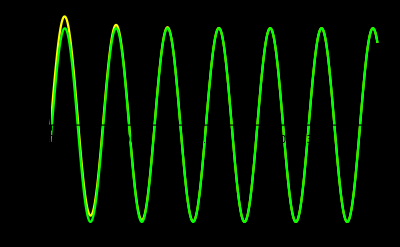

```mathematica
ClearAll["Global*`"];
ux[t_] := Um*Sin[ω*t+φ];
U = Um*Exp[ⅉ*φ];

Um = 12.5;
ω = 10^5;
φ = 1.2;

R1 = 10 * 10^3;
R2 = 10 * 10^3;
C1 = 10* 10^-9;
tmax = 0.0004;

(* Klasické řešení NDSolvem *)
rovnice = {
0 == iu[t] + ir1[t],
ir1[t] == ic1[t] + ir2[t],
ux[t] == u1[t],
u1[t]-u2[t] == R1 * ir1[t],
ic1[t] == C1 * u2'[t],
u2[t] == R2 * ir2[t],
u2[0] == 0
};
promenne = Union[Cases[rovnice, _Symbol[t], {0, Infinity}]]; 
reseni = NDSolve[rovnice, promenne, {t, 0, tmax}, StartingStepSize-> 10^-9];

(* Nyní vykreslení HUS *)
rovniceHUS = {
0 == iu + ir1,
ir1 == ic1 + ir2,
U == u1,
u1 - u2 == R1 * ir1,
ic1 == C1 * ⅉ * ω * u2,
u2 == R2 * ir2
};
reseniHUS = Solve[rovniceHUS];

(* Vykreslení grafu - pozor na parametry *)
Plot[{u2[t] /. reseni[[1]], Im[u2 * Exp[ⅉ * ω * t]] /. reseniHUS}, {t, 0, tmax}, PlotStyle -> {Yellow, Green}, PlotLegends -> "u2(t)", Background -> Black, PlotRange -> All]
```